```mathematica
Clear["Global`*"]
SetDirectory[NotebookDirectory[]];
```

```mathematica
map[x_,y_,μ_]= ComplexExpand[μ (x+I*y)(1-(x+I*y))]
```

3.84 x-3.84 x^2+3.84 y^2+ⅈ (3.84 y-7.68 x y)

```mathematica
f1=NSolve[{x μ-x^2 μ+y^2 μ==x,y μ-2 x y μ==y},{x,y}]
```

{{x→0.739583,y→0.},{x→0.369792,y→0.-0.369792 ⅈ},{x→0.369792,y→0.+0.369792 ⅈ},{x→0.,y→0.}}

```mathematica
f1/. μ-> 1.1
```

{{x→0,y→0},{x→0.0454545,y→0.-0.0454545 ⅈ},{x→0.0454545,y→0.+0.0454545 ⅈ},{x→0.0909091,y→0}}

```mathematica
FindRoot[Re[map[x,y,2]]==x,Im[map[x,y,2]==y],{{x,0.5},{y,0}}]
```

FindRoot::fdssnv: Search specification Im[map[x,y,2]==y] without variables should be a list with 1 to 4 elements.

FindRoot[Re[map[x,y,2]]==x,Im[map[x,y,2]==y],{{x,0.5},{y,0}}]

```mathematica
s={Re[map[x,y,μ]],Im[map[x,y,μ]]}/. {x-> 0.9,y-> 0.1,μ-> 2}
s⟦1⟧
```

{-1.42,-0.52}

-1.42

```mathematica
Mx={};
My={};
μ=2;
x=0.9;
y=3 10^-1;
For[i=1,i<50,i++;
m1={Re[map[x,y,μ]],Im[map[x,y,μ]]};
x=m1⟦1⟧;
y=m1⟦2⟧;
Mx=Append[Mx,{i,x}];
My=Append[My,{i,y}];
]
p1=ListPlot[{Mx,My},Frame->True,PlotLabel->μ,Joined->True];
Mx={};
My={};
μ=2;
x=0.9;
y=1 10^-1;
For[i=1,i<50,i++;
m1={Re[map[x,y,μ]],Im[map[x,y,μ]]};
x=m1⟦1⟧;
y=m1⟦2⟧;
Mx=Append[Mx,{i,x}];
My=Append[My,{i,y}];
]
p2=ListPlot[{Mx,My},Frame->True,PlotLabel->Row[{"μ=",μ}],Joined->True];
Show[p1,p2]
```

ListPlot::prng: Value of option PlotRange -> {{0,50.},{-3.92100407244630385968636308808073807416`15.954473213853419*^5007942945,2.3526024434677823158118178528484428445`15.954589770191005*^5007942945}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ListPlot::prng: Value of option PlotRange -> {{0,50.},{-2.37115909880642×10^500969486,1.42269545928385×10^500969486}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

-Graphics-

```mathematica
Mx={};
My={};
μ=2+10^-8;
x=0.9;
y=3 10^-1;
For[i=1,i<50,i++;
m1={Re[map[x,y,μ]],Im[map[x,y,μ]]};
x=m1⟦1⟧;
y=m1⟦2⟧;
Mx=Append[Mx,{i,x}];
My=Append[My,{i,y}];
]
p1=ListPlot[{Mx,My},Frame->True,PlotLabel->μ,Joined->True];
Mx={};
My={};
x=0.9;
y=1 10^-1;
For[i=1,i<50,i++;
m1={Re[map[x,y,μ]],Im[map[x,y,μ]]};
x=m1⟦1⟧;
y=m1⟦2⟧;
Mx=Append[Mx,{i,x}];
My=Append[My,{i,y}];
]
p2=ListPlot[{Mx,My},Frame->True,Joined->True];
Show[p1,p2,PlotRange-> {-1,1},PlotLabel->Row[{"μ=",N[μ,9]}]]
```

ListPlot::prng: Value of option PlotRange -> {{0,50.},{-3.92100407244630385968636308808073807416`15.954473213853419*^5007942945,2.3526024434677823158118178528484428445`15.954589770191005*^5007942945}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ListPlot::prng: Value of option PlotRange -> {{0,50.},{-2.37115909880642×10^500969486,1.42269545928385×10^500969486}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

-Graphics-

```mathematica
map2[x_,y_,μ_]=ComplexExpand[map[Re[map[x,y,μ]],Im[map[x,y,μ]],μ]]
```

1.79412377275333245389015282256669421854`15.728817273443019*^262652290228812+2.30744870869153078878410368076433732842`14.336553543497105*^262652290228812 ⅈ

```mathematica
x μ^2-x^2 μ^2+y^2 μ^2-x^2 μ^3+2 x^3 μ^3-x^4 μ^3+y^2 μ^3-6 x y^2 μ^3+6 x^2 y^2 μ^3-y^4 μ^3+ⅈ (y μ^2-2 x y μ^2-2 x y μ^3+6 x^2 y μ^3-4 x^3 y μ^3-2 y^3 μ^3+4 x y^3 μ^3)
```

2.534829315842789199935691460401743295`13.47109230596316*^262652290228811+3.2600808932032564627144326947853518528`13.583978554337152*^262652290228811 ⅈ

```mathematica
map2[1,1,2]
```

4+12 ⅈ

```mathematica
map3[x_,y_,μ_]=ComplexExpand[map[Re[map2[x,y,μ]],Im[map2[x,y,μ]],μ]]
```

8.08488741612887719004739425329143410913`15.277272279947047*^525304580457624-3.179403711492445230130729783068125891473`14.298924794039108*^525304580457625 ⅈ

```mathematica
s3:=Solve[{x μ^3-x^2 μ^3+y^2 μ^3-x^2 μ^4+2 x^3 μ^4-x^4 μ^4+y^2 μ^4-6 x y^2 μ^4+6 x^2 y^2 μ^4-y^4 μ^4-x^2 μ^5+2 x^3 μ^5-x^4 μ^5+y^2 μ^5-6 x y^2 μ^5+6 x^2 y^2 μ^5-y^4 μ^5+2 x^3 μ^6-6 x^4 μ^6+6 x^5 μ^6-2 x^6 μ^6-6 x y^2 μ^6+36 x^2 y^2 μ^6-60 x^3 y^2 μ^6+30 x^4 y^2 μ^6-6 y^4 μ^6+30 x y^4 μ^6-30 x^2 y^4 μ^6+2 y^6 μ^6-x^4 μ^7+4 x^5 μ^7-6 x^6 μ^7+4 x^7 μ^7-x^8 μ^7+6 x^2 y^2 μ^7-40 x^3 y^2 μ^7+90 x^4 y^2 μ^7-84 x^5 y^2 μ^7+28 x^6 y^2 μ^7-y^4 μ^7+20 x y^4 μ^7-90 x^2 y^4 μ^7+140 x^3 y^4 μ^7-70 x^4 y^4 μ^7+6 y^6 μ^7-28 x y^6 μ^7+28 x^2 y^6 μ^7-y^8 μ==x,y μ^3-2 x y μ^3-2 x y μ^4+6 x^2 y μ^4-4 x^3 y μ^4-2 y^3 μ^4+4 x y^3 μ^4-2 x y μ^5+6 x^2 y μ^5-4 x^3 y μ^5-2 y^3 μ^5+4 x y^3 μ^5+6 x^2 y μ^6-24 x^3 y μ^6+30 x^4 y μ^6-12 x^5 y μ^6-2 y^3 μ^6+24 x y^3 μ^6-60 x^2 y^3 μ^6+40 x^3 y^3 μ^6+6 y^5 μ^6-12 x y^5 μ^6-4 x^3 y μ^7+20 x^4 y μ^7-36 x^5 y μ^7+28 x^6 y μ^7-8 x^7 y μ^7+4 x y^3 μ^7-40 x^2 y^3 μ^7+120 x^3 y^3 μ^7-140 x^4 y^3 μ^7+56 x^5 y^3 μ^7+4 y^5 μ^7-36 x y^5 μ^7+84 x^2 y^5 μ^7-56 x^3 y^5 μ^7-4 y^7 μ^7+8 x y^7 μ^7==y}/. μ-> 2,{x,y}]
```

```mathematica
Length[s3]
```

64

```mathematica
Plot[s3⟦All,1,2⟧,{μ,1,4}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

$Aborted

```mathematica
map3[1,0.1,3]
```

map3[1,0.1,3]

```mathematica
s1=Solve[{Re[map[x,y,μ]]== x,Im[map[x,y,μ]]== y},{x,y}  ]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

Solve::fdimc: When parameter values satisfy the condition «1», the solution set contains a full-dimensional component; use Reduce for complete solution information.

{{x→ConditionalExpression[0,(Im[y]==0&&-1/Im[μ]+2 Re[y]+√((-1+Re[μ])^2/Im[μ]^2)+Re[μ]/Im[μ]==0&&Im[μ]>0&&0<Re[μ]<1&&-Im[μ]+√(-(-1+Re[μ]) Re[μ])>0)||(Im[y]==0&&-1/Im[μ]+2 Re[y]+√((-1+Re[μ])^2/Im[μ]^2)+Re[μ]/Im[μ]==0&&0<Re[μ]<1&&-Im[μ]+√(-(-1+Re[μ]) Re[μ])<0)]}}

```mathematica
tab1=Table[NSolve[{Re[map[x,y,μ]]== x,Im[map[x,y,μ]]== y},{x,y},Reals],{μ,1,4}]
```

NSolve::ivar: -2.523528790233939357937708665782873`15.68178133662052*^65663072557202 is not a valid variable.

General::stop: Further output of NSolve::ivar will be suppressed during this calculation.

{NSolve[{False,False},{-2.523528790233939357937708665782873`15.68178133662052*^65663072557202,-4.043736039617885765552370587922202`14.364775105590603*^65663072557202},ℝ],NSolve[{False,False},{-2.523528790233939357937708665782873`15.68178133662052*^65663072557202,-4.043736039617885765552370587922202`14.364775105590603*^65663072557202},ℝ],NSolve[{False,False},{-2.523528790233939357937708665782873`15.68178133662052*^65663072557202,-4.043736039617885765552370587922202`14.364775105590603*^65663072557202},ℝ],NSolve[{False,False},{-2.523528790233939357937708665782873`15.68178133662052*^65663072557202,-4.043736039617885765552370587922202`14.364775105590603*^65663072557202},ℝ]}

```mathematica
Table[NSolve[{Re[map[x,y,μ]]== x,Im[map[x,y,μ]]== y},{x,y},Reals],{μ,1,4}]⟦All,1⟧
```

{{x→0,y→0},{x→0,y→0},{x→0,y→0},{x→0,y→0}}

```mathematica
tab2=Delete[tab1,1]
```

{{{x→0,y→0},{x→0.5,y→0}},{{x→0,y→0},{x→0.666667,y→0}},{{x→0,y→0},{x→0.75,y→0}}}

```mathematica
tab2⟦All,2⟧
```

{{x→0.5,y→0},{x→0.666667,y→0},{x→0.75,y→0}}

```mathematica
tab2⟦All,2,2,2⟧
```

{0,0,0}

```mathematica
l=FindRoot[{Re[map[x,y,μ]]== x,Im[map[x,y,μ]]== y},{{x,0.5},{y,0.1}}]/. μ-> 2.3
```

{x→0.75,y→-3.97675×10^-20}

```mathematica
l⟦1,2⟧
```

0.75

```mathematica
l2=Flatten[Delete[l,1]]
```

{x→0.565217,y→0.}

```mathematica
Extract[1][l2⟦All,2⟧]
```

0.565217

```mathematica
Lx={};
Ly={};
For[i=1,i<40,i++;
μ=i/10;
tab1=FindRoot[{Re[map[x,y,μ]]== x,Im[map[x,y,μ]]== y},{{x,0.9},{y,0.9}}];
Lx=Append[Lx,{μ,tab1⟦1,2⟧}];
Ly=Append[Ly,{μ,tab1⟦2,2⟧}];
]
```

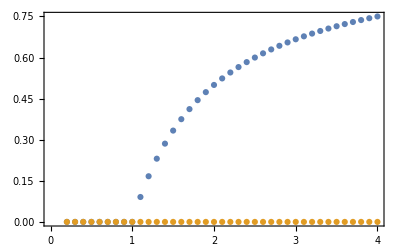

```mathematica
ListPlot[{Lx,Ly},Frame->True]
```

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

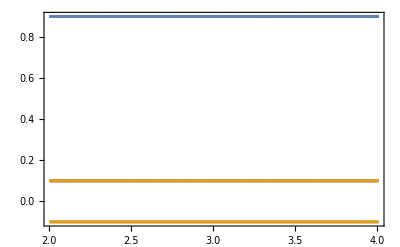

```mathematica
Lx={};
Ly={};
For[i=200,i<400,i++;
μ=i/100;
tab1=FindRoot[{Re[map3[x,y,μ]]== x,Im[map3[x,y,μ]]== y},{{x,0.9},{y,0.1}}];
Lx=Append[Lx,{μ,tab1⟦1,2⟧}];
Ly=Append[Ly,{μ,tab1⟦2,2⟧}];
tab1=FindRoot[{Re[map3[x,y,μ]]== x,Im[map3[x,y,μ]]== y},{{x,0.9},{y,-0.1}}];
Lx=Append[Lx,{μ,tab1⟦1,2⟧}];
Ly=Append[Ly,{μ,tab1⟦2,2⟧}];
tab1=FindRoot[{Re[map3[x,y,μ]]== x,Im[map3[x,y,μ]]== y},{{x,0.1},{y,0.1}}];
Lx=Append[Lx,{μ,tab1⟦1,2⟧}];
Ly=Append[Ly,{μ,tab1⟦2,2⟧}];
tab1=FindRoot[{Re[map3[x,y,μ]]== x,Im[map3[x,y,μ]]== y},{{x,0.1},{y,-0.1}}];
Lx=Append[Lx,{μ,tab1⟦1,2⟧}];
Ly=Append[Ly,{μ,tab1⟦2,2⟧}];
]
ListPlot[{Lx,Ly},Frame->True]
```

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

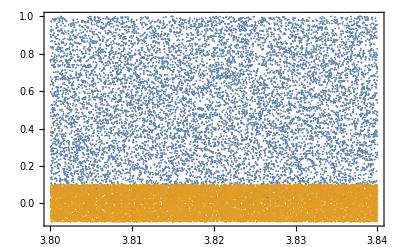

```mathematica
Lx={};
Ly={};
For[i=3.8 30000,i<3.84 30000,i++;
μ=i/30000;
For[j=1,j<10,j++;
x0=RandomReal[];
y0=RandomReal[] 10^-1;
tab1=FindRoot[{Re[map3[x,y,μ]]== x,Im[map3[x,y,μ]]== y},{{x,x0},{y,y0}}];
Lx=Append[Lx,{μ,tab1⟦1,2⟧}];
Ly=Append[Ly,{μ,tab1⟦2,2⟧}];
tab1=FindRoot[{Re[map3[x,y,μ]]== x,Im[map3[x,y,μ]]== y},{{x,x0},{y,-y0}}];
Lx=Append[Lx,{μ,tab1⟦1,2⟧}];
Ly=Append[Ly,{μ,tab1⟦2,2⟧}];
]
]
ListPlot[{Lx,Ly},Frame->True]
```

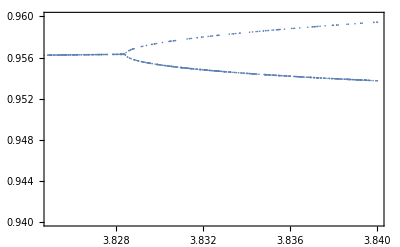

```mathematica
ListPlot[{Lx,Ly},Frame->True,PlotRange->{{3.825,3.84},{0.94,0.96}}]
```

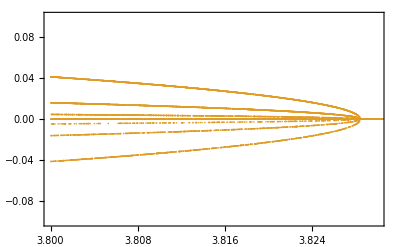

```mathematica
ListPlot[{Lx,Ly},Frame->True,PlotRange->{{3.8,3.83},{-0.1,0.1}}]
```

Agora, antes da abertura da janela Real, conhecemos os pontos fixos complexos do map3.
Só falta calcular os autovalores do mapa linearizado nestes pontos (em função de μ). Note que o cálculo deve ser numérico e feito para cada valor de μ, já que não temos uma expressão analítica para estes pontos fixos.

```mathematica
Lx⟦⟧
```

{3.80003,0.736844}

```mathematica
Ly⟦1⟧
```

```mathematica
{3.8000333333333334,-6.62863768808783*^-20}
```

```mathematica
Lx⟦1⟧
```

{3.80003,0.300482}

```mathematica
Lx⟦1⟧

Lx⟦1⟧
```

{3.80003,0.300482}

{3.80003,0.300482}